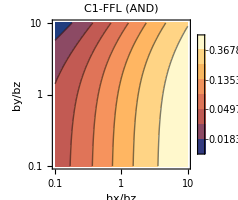
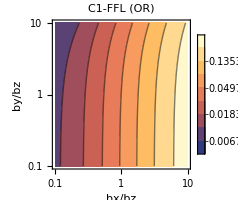
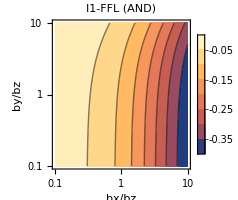
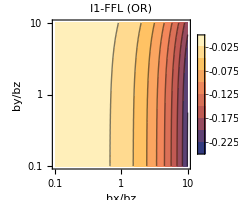
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*
Notations: xav=<x>, yav=<y>, zav=<z>
		fijp=Subscript[f, ij]'
*)
(*------Squared coefficient of variation: Subscript[CV^2, i]=Subscript[σ^2, i]/(<i>^2), Subscript[CV^2, ij]=Subscript[σ^2, ij]/(<i><j>)------*)

Γxy=(1+bx)/(βx+βy);
Γxz=(1+bx)/(βx+βz);
Γyz=(1+by)/(βy+βz);
Γxyz1=(1+bx)/((βx+βy)*(βx+βz));
Γxyz2=((1+bx)*(βx+βy+βz))/(βy*(βx+βy)*(βx+βz)*(βy+βz));
Γxyz3=((1+bx)*(2*βx+βy+βz))/((βx+βy)*(βx+βz)*(βy+βz));



ηxy=Γxy/yav*fyxp; (*Subscript[η^2, xy]*)

ηxz1=Γxz/zav*fzxp; (*Subscript[η^2, xz,d]*)
ηxz2=Γxyz1/zav*fyxp*fzyp; (*Subscript[η^2, xz,ind]*)
ηxz=ηxz1+ηxz2; (*Subscript[η^2, xz]*)

ηyz1=Γyz/zav*fzyp; (*Subscript[η^2, yz,Subscript[ind, 1]]*)
ηyz2=(Γxyz2*xav)/(yav*zav)*fyxp^2*fzyp; (*Subscript[η^2, yz,Subscript[ind, 2]]*)
ηyz3=(Γxyz3*xav)/(yav*zav)*fyxp*fzxp; (*Subscript[η^2, yz,cross]*)
ηyz=ηyz1+ηyz2+ηyz3; (*Subscript[η^2, yz]*)



ηzi=(1+bz)/zav; (*Subscript[η^2, z,int]*)

ηzd=(fzxp*xav)/(βz*zav)*ηxz1; (*Subscript[η^2, z,d]*)

ηzind=(fzyp*yav)/(βz*zav)*(ηyz1+ηyz2); (*Subscript[η^2, z,ind]*)

prefactor1=(fzxp*xav)/(βz*zav);
ηzsyn1=prefactor1*ηxz2; 
prefactor2=(fzyp*yav)/(βz*zav);
ηzsyn2=prefactor2*ηyz3; 
ηzsyn=ηzsyn1+ηzsyn2; (*Subscript[η^2, z,cross]*)

ηp=ηzi+ηzd+ηzind; (*Subscript[η^2, z,path]*)

ηz=ηp+ηzsyn; (*Subscript[η^2, z]*)

ηr=ηzsyn/ηp; (*Relative synergy noise*)


(*------Particular motifs and their functions------*)
(*C1-FFL-AND*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
xav=100; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/(fyx*(1+by)); αz=(βz*zav)/(fzx*fzy*(1+bz));
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*(1+by)*Kxy/(Kxy+xav)^2;fzxp=αz*(1+bz)*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*(1+bz)*fzx*Kyz/(Kyz+yav)^2;

(*Fig 3c*)
ηrca=ηr;

(*I1-FFL-AND*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
xav=100; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=200;

αy= (βy*yav)/(fyx*(1+by)); αz=(βz*zav)/(fzx*fzy*(1+bz));
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*(1+by)*Kxy/(Kxy+xav)^2;fzxp=αz*(1+bz)*fzy*Kxz/(Kxz+xav)^2; fzyp=αz*(1+bz)*fzx*-Kyz/(Kyz+yav)^2;

(*Fig 3c*)
ηria=ηr;

(*C1-FFL-OR*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
xav=100; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=100;

αy= (βy*yav)/(fyx*(1+by)); αz=(βz*zav)/((fzx+fzy)*(1+bz));
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=yav/(Kyz+yav);
fyxp=αy*(1+by)*Kxy/(Kxy+xav)^2;fzxp=αz*(1+bz)*Kxz/(Kxz+xav)^2; fzyp=αz*(1+bz)*Kyz/(Kyz+yav)^2;

(*Fig S4*)
ηrco=ηr;

(*I1-FFL-OR*)
Clear[Kxy,Kxz,Kyz,αy,αz,fyx,fzx,fzy,fyxp,fzxp,fzyp,βx,βy,βz,xav,yav,zav];

βx=0.1; βy=1.0; βz=10.0;
xav=100; yav=100; zav=100;
Kxy=100; Kxz=100; Kyz=200;

αy= (βy*yav)/(fyx*(1+by)); αz=(βz*zav)/((fzx+fzy)*(1+bz));
fyx=xav/(Kxy+xav); fzx=xav/(Kxz+xav); fzy=Kyz/(Kyz+yav);
fyxp=αy*(1+by)*Kxy/(Kxy+xav)^2;fzxp=αz*(1+bz)*Kxz/(Kxz+xav)^2; fzyp=αz*(1+bz)*-Kyz/(Kyz+yav)^2;

(*Fig S4*)
ηrio=ηr;
(********************************************************)
Clear[bx,by,bz];
bz=10;
bx=rxz*bz; by=ryz*bz;

rxzi=0.1; rxzf=10; ryzi=0.1; ryzf=10;

p1=ContourPlot[ηrca,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"bx/bz","by/bz"},ImageSize->200,PlotLabel->"C1-FFL (AND)",PlotLegends->Automatic,ScalingFunctions->{"Log","Log","Log"}];

p2=ContourPlot[ηrco,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"bx/bz","by/bz"},ImageSize->200,PlotLabel->"C1-FFL (OR)",PlotLegends->Automatic,ScalingFunctions->{"Log","Log","Log"}];

p3=ContourPlot[ηria,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"bx/bz","by/bz"},ImageSize->200,PlotLabel->"I1-FFL (AND)",PlotLegends->Automatic,ScalingFunctions->{"Log","Log",None}];

p4=ContourPlot[ηrio,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"bx/bz","by/bz"},ImageSize->200,PlotLabel->"I1-FFL (OR)",PlotLegends->Automatic,ScalingFunctions->{"Log","Log",None}];

Grid[{{p1,p2,p3,p4}}]

(*Data Extraction*)

toEString[dat_]:=If[dat==0.,"0.0000000000000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];

rxzi=0.1;           (*start*)
rxzk=1;             (*switching point*)
rxzf=10;            (*final*)
rxzRange=Join[Range[rxzi,rxzk,0.01],Range[rxzk+0.1,rxzf,0.1]];

ryzi=0.1;           (*start*)
ryzk=1;             (*switching point*)
ryzf=10;            (*final*)
ryzRange=Join[Range[ryzi,ryzk,0.001],Range[ryzk+0.01,ryzf,0.01]];


t1=Flatten[Table[{rxz,ryz,ηrca},{rxz,rxzRange},{ryz,ryzRange}],1];
tp1=StringJoin@Map[(toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n")&,t1];
Export["F:\\Colab\\FFL-CT\\Burst\\rxz-ryz-relsyn-c1and.dat",tp1];

t1=Flatten[Table[{rxz,ryz,ηrco},{rxz,rxzRange},{ryz,ryzRange}],1];
tp1=StringJoin@Map[(toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n")&,t1];
Export["F:\\Colab\\FFL-CT\\Burst\\rxz-ryz-relsyn-c1or.dat",tp1];

t1=Flatten[Table[{rxz,ryz,ηria},{rxz,rxzRange},{ryz,ryzRange}],1];
tp1=StringJoin@Map[(toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n")&,t1];
Export["F:\\Colab\\FFL-CT\\Burst\\rxz-ryz-relsyn-i1and.dat",tp1];

t1=Flatten[Table[{rxz,ryz,ηrio},{rxz,rxzRange},{ryz,ryzRange}],1];
tp1=StringJoin@Map[(toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n")&,t1];
Export["F:\\Colab\\FFL-CT\\Burst\\rxz-ryz-relsyn-i1or.dat",tp1];

(*t1=Table[{rxz,ryz,ηrca},{rxz,rxzi,rxzf,0.01},{ryz,ryzi,ryzf,0.01}]
tp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@t1];
Export["F:\\Colab\\FFL-CT\\Burst\\rxz-ryz-relsyn-c1and.dat",tp1,"FieldSeparators"->"    "];*)

(*Clear[bx,by,bz];

bz=10; bx=10;
byi=0; byf=100;

p5=Plot[{ηrca,ηrco,ηria,ηrio},{by,byi,byf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick},{Blue,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"by","Relative synergy"},ImageSize->250,PlotLegends->{"C1-FFL (AND)","C1-FFL  (OR)","I1-FFL (AND)","I1-FFL (OR)"},PlotRange->All];

Clear[bx,by,bz];

bz=10; by=10;
bxi=0; bxf=100;

p6=Plot[{ηrca,ηrco,ηria,ηrio},{bx,bxi,bxf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick},{Blue,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"bx","Relative synergy"},ImageSize->250,PlotLegends->{"C1-FFL (AND)","C1-FFL  (OR)","I1-FFL (AND)","I1-FFL (OR)"},PlotRange->All];

Clear[bx,by,bz];

bx=10; by=10;
bzi=0; bzf=100;

p7=Plot[{ηrca,ηrco,ηria,ηrio},{bz,bzi,bzf},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Green,Thick},{Red,Thick},{Blue,Thick},{Black,Thick}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"bz","Relative synergy"},ImageSize->250,PlotLegends->{"C1-FFL (AND)","C1-FFL  (OR)","I1-FFL (AND)","I1-FFL (OR)"},PlotRange->All];

Clear[bx,by,bz,rxz,ryz];
bx=10; 
by=rxz*bx; bz=ryz*bx;

rxzi=0.5; rxzf=2; ryzi=0.5; ryzf=2;


p8=ContourPlot[ηrca,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"by/bx","bz/bx"},ImageSize->300,PlotLabel->"C1-FFL (AND)",PlotLegends->Automatic];

p9=ContourPlot[ηrco,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"by/bx","bz/bx"},ImageSize->300,PlotLabel->"C1-FFL (OR)",PlotLegends->Automatic];

p10=ContourPlot[ηria,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"by/bx","bz/bx"},ImageSize->300,PlotLabel->"I1-FFL (AND)",PlotLegends->Automatic];

p11=ContourPlot[ηrio,{rxz,rxzi,rxzf},{ryz,ryzi,ryzf},Frame->True,FrameStyle->Directive[Black,Thick],BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"by/bx","bz/bx"},ImageSize->300,PlotLabel->"I1-FFL (OR)",PlotLegends->Automatic];

Grid[{{p1,p2},{p3,p4},{p5,p6,p7},{p8,p9},{p10,p11}}]*)

Quit[];
```